## Computing for Mathematical Physics 2021/22

# Homework 2

# Mark for homework 2: /28 (to be completed by your marker)

# Feedback from marker: (to be completed by your marker)

# Give your answers in the code cells marked (* Enter your solution here *)

Data for use in questions 1 and 2.

• The exercises make use of the following lists.
• Execute the following three input cells with ⇧+⌤ before attempting the questions.
• Do not edit the data below in any way.

The following cell contains data on the planets. It will be used in question 1.

```mathematica
(* Planet data entries: name, type, mean radius (km), mass (kg) *)
planetaryData={
{"Mercury","Terrestrial", 2439.7,3.3011*10^23},
{"Venus","Terrestrial", 6051.8,4.8675*10^24},
{"Earth","Terrestrial",6371.0,5.9724*10^24},
{"Mars","Terrestrial",3389.5,6.4171*10^23},
{"Jupiter","Gas Giant",69911,1.8982*10^27},
{"Saturn","Gas Giant",58232,5.6834*10^26},
{"Uranus","Ice Giant",25362,8.6810*10^25},
{"Neptune","Ice Giant",24622,1.0241*10^26}
};
```

The following code snippet creates a list containing the first 100,000 digits of π, storing it as piDigits. This is to be modified in question 2.

```mathematica
piDigits=RealDigits[N[π,100000]][[1]];
```

The following function is also for use in question 2. It takes a list as input and returns True if the length of the list is 1, and False otherwise.

```mathematica
lengthIsOneQ[sublist_]:=(Length[sublist]==1);
```

Questions
Double click the vertical braces on the RHS of each of the three question headings to open and view them.

1. Manipulating data. [10 marks]

The entries in planetaryData, in the section of the notebook above titled Data for use in questions 1 and 2, each comprise of a planet name, along with its type, mean radius (km), and mass (kg). In this question we will perform various manipulations on this data. Your answers should not use any manual/by-hand manipulations of the list, but instead must be carried out with Mathematica’s list manipulation functions.

a) Using Transpose and an appropriate value within the [[...]] operator, generate a new list from planetaryData containing only the names of the planets. Use Sort[...] to put the list in alphabetical order.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
Clear["Global`*"];
planetaryData={
{"Mercury","Terrestrial", 2439.7,3.3011*10^23},
{"Venus","Terrestrial", 6051.8,4.8675*10^24},
{"Earth","Terrestrial",6371.0,5.9724*10^24},
{"Mars","Terrestrial",3389.5,6.4171*10^23},
{"Jupiter","Gas Giant",69911,1.8982*10^27},
{"Saturn","Gas Giant",58232,5.6834*10^26},
{"Uranus","Ice Giant",25362,8.6810*10^25},
{"Neptune","Ice Giant",24622,1.0241*10^26}
};
```

```mathematica
planetNames = Transpose[planetaryData][[1]]
planetNames = Sort[planetNames]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

{Earth,Jupiter,Mars,Mercury,Neptune,Saturn,Uranus,Venus}

b) Use Count, with an appropriate level-specification, to find the number of planets of each type. Present the results in a list of the form {{“Terrestrial”, no. of terrestrials}, {“Gas Giant”, no. of Gas Giants}, {“Ice Giant”, no. of ice giants}}.
[Hint: consider the output from applying Treeform to planetaryData, to help understand the correct level parameter to use with Count.]
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

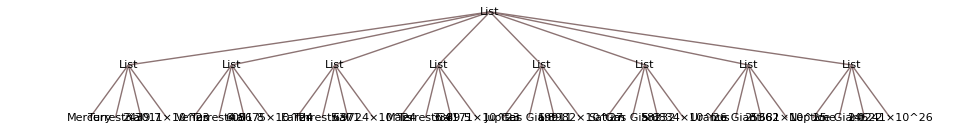

{{Terrestrial,4},{Gas Giant,2},{Ice Giant,2}}

```mathematica
TreeForm[planetaryData]
planetTypes = {{"Terrestrial",Count[planetaryData, "Terrestrial",2]}, {"Gas Giant",Count[planetaryData, "Gas Giant",2] },{"Ice Giant", Count[planetaryData, "Ice Giant",2]}}
```

c) Sort the entries in planetaryData from smallest to largest mass. Do this by first using RotateRight, with an appropriate level specification, to shuffle the data structure such that the masses appear as the first column, then apply Sort, and finally undo the initial shuffling with RotateRight by an appropriate call to RotateLeft.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
planetsMassSorted = RotateLeft[Sort[RotateRight[planetaryData, {0,1}]], {0,1}]
```

{{Mercury,Terrestrial,2439.7,3.3011×10^23},{Mars,Terrestrial,3389.5,6.4171×10^23},{Venus,Terrestrial,6051.8,4.8675×10^24},{Earth,Terrestrial,6371.,5.9724×10^24},{Uranus,Ice Giant,25362,8.681×10^25},{Neptune,Ice Giant,24622,1.0241×10^26},{Saturn,Gas Giant,58232,5.6834×10^26},{Jupiter,Gas Giant,69911,1.8982×10^27}}

d) Use Transpose, or alternatively the Span operator ‘;;’, to extract three separate lists (columns) from the planetaryData data structure: planetaryNames, comprising just the names of the planets, planetaryRadii comprising just their radii (km), and planetaryMasses comprising just their masses (kg). Using the latter three lists, construct a new list of the form {{planet name 1, density 1}, {planet name 2, density 2}, ...}, where the density should be given in g/cm^3, according to the formula M_planet/(4/3 π R_planet^3), wherein M_planet denotes a planet’s mass in g, and R_planet its radius in cm. 
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
planetaryNames =Transpose[planetaryData][[1]];
planetaryRadii = Transpose[planetaryData][[3]];
planetaryMasses = Transpose[planetaryData][[4]];
planetaryDensity = {};
For[i=1, i< Length[planetaryMasses]+1, i++, AppendTo[planetaryDensity, planetaryMasses[[i]]*1000/(4/3 Pi (planetaryRadii[[i]] * 10^5)^3)]];
planetaryNameDensity = {};
For [i =1, i < Length[planetaryNames]+1, i++, AppendTo[planetaryNameDensity, {planetaryNames[[i]], planetaryDensity[[i]]}]];
planetaryNameDensity
```

{{Mercury,5.42701},{Venus,5.2428},{Earth,5.51363},{Mars,3.93408},{Jupiter,1.32622},{Saturn,0.687123},{Uranus,1.27037},{Neptune,1.63789}}

2. Searching for and analysing sequences of identical elements in a list. [6 marks]

a) Modify the code used to create a list of the first 100,000 digits in π, found in the section of the notebook above titled Data for use in questions 1 and 2, to obtain a new list, eulerDigits, containing the first 100,000 digits in Euler’s constant, 0.577216... , known to Mathematica as EulerGamma. You can ignore the leading zero in Euler’s constant, i.e. your list should contain 100,000 elements, the first of which is 5. Suppress the full list output by terminating any relevant commands with a semi-colon. Display instead just the first 8 elements with eulerDigits[[1;;8]].
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
Clear["Global`*"];
lengthIsOneQ[sublist_]:=(Length[sublist]==1);
```

```mathematica
eulerDigits=RealDigits[N[EulerGamma, 100000]][[1]];
eulerDigits[[1;;8]]
```

{5,7,7,2,1,5,6,6}

b) Use Partition with eulerDigits to create a new list partitionedEulerDigits, comprised of 99,998 three-element sublists, starting { {5,7,7}, {7,7,2}, {7,2,1}, {2,1,5}, {1,5,6}, ... }. I.e. the partitioning of eulerDigits is such that the second & third numbers in each sublist, reappear again as the first & second numbers in the following sublist. Suppress the full list output by terminating any relevant commands with a semi-colon. Display instead just the first 6 elements with partitionedEulerDigits[[1;;6]].
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
partitionedEulerDigits=Partition[eulerDigits,3,1];
partitionedEulerDigits[[1;;6]]
```

{{5,7,7},{7,7,2},{7,2,1},{2,1,5},{1,5,6},{5,6,6}}

c) Using Map[...] apply Union[...] to each of the three-element sublists in partitionedEulerDigits, to create a new list called partitionedEulerDigitsReduced. In this new list any three-element sublists made of three identical digits in partitionedEulerDigits will have been replaced by one-element sublists. Similarly, any three-element sublists in partitionedEulerDigits containing two identical digits will have been replaced by two-element sublists. Suppress any verbose list output by terminating any relevant commands with a semi-colon. Instead, display just the first 6 elements of the result with partitionedEulerDigitsReduced[[1;;6]].
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
partitionedEulerDigitsReduced=Map[Union, partitionedEulerDigits];
partitionedEulerDigitsReduced[[1;;6]]
```

{{5,7},{2,7},{1,2,7},{1,2,5},{1,5,6},{5,6}}

d) The function lengthIsOneQ defined in the section of the notebook above titled Data for use in questions 1 and 2, returns True when passed a (sub)list of length 1, and False otherwise. Use lengthIsOneQ with Select[...] to produce a list of all sublists of length 1 residing in partitionedEulerDigitsReduced (suppress the full list output with a semi-colon). Hence, determine the number of times that three consecutive digits are the same, in the first 100,000 digits of Euler’s constant. 
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
EulerDigits1Length=Select[partitionedEulerDigitsReduced, lengthIsOneQ];
Length[EulerDigits1Length]
```

962

e) Generalise parts b), c), d) to determine the number of times that six consecutive digits are the same, in the first 100,000 digits of Euler’s constant. 
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
partitionedEulerDigits6 = Partition[eulerDigits,6,1];
partitionedEulerDigits6[[1;;6]]
partitionedEulerDigits6Reduced=Map[Union, partitionedEulerDigits6];
partitionedEulerDigits6Reduced[[1;;6]]
EulerDigits6Length1=Select[partitionedEulerDigits6Reduced, lengthIsOneQ];
Length[EulerDigits6Length1]
```

{{5,7,7,2,1,5},{7,7,2,1,5,6},{7,2,1,5,6,6},{2,1,5,6,6,4},{1,5,6,6,4,9},{5,6,6,4,9,0}}

{{1,2,5,7},{1,2,5,6,7},{1,2,5,6,7},{1,2,4,5,6},{1,4,5,6,9},{0,4,5,6,9}}

2

3. Basic combinatorial analysis using lists with Outer, Flatten, Map, Union, Count, etc.  [12 marks]

a) Use Outer, List, and Flatten, together with the list {1,2,3,4,5,6,7,8} to generate a new list, possibleOutcomes, which shows the possible outcomes of throwing three eight-sided dice, in the form {{1,1,1},{1,1,2},...}. Note, Outer can take four input arguments, e.g. Outer[Times,{a,b},{c,d},{e,f}].

Suppress verbose list output by terminating any relevant commands with a semi-colon. Display instead just the first six elements with possibleOutcomes[[1;;6]].

How many possibilities are there? Store this number as numberOfPossibleOutcomes.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
Clear["Global`*"]
```

```mathematica
numList = {1,2,3,4,5,6,7,8};
twopossibleOutcomes =Outer[List,numList,numList];
twopossibleOutcomes=Flatten[twopossibleOutcomes,1];
possibleOutcomes = Partition[Flatten[Outer[List, numList,twopossibleOutcomes,1]],3];
possibleOutcomes[[1;;6]]
numberOfPossibleOutcomes =Length[possibleOutcomes]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6}}

512

b) Use Map[...] with Total[...] and possibleOutcomes to create a list, possibleTotals, where each element is given by the sum of the three dice-rolls in the corresponding element of possibleOutcomes. Suppress verbose list output by terminating any relevant commands with a semi-colon. Display instead just the last six elements with possibleTotals[[-6;;-1]].
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
possibleTotals=Map[Total, possibleOutcomes];
possibleTotals[[-6;;-1]]
```

{19,20,21,22,23,24}

c) Use Union[...] to create a list of all distinct possible totals, distinctPossibleTotals, from  possibleTotals, sorted in increasing order. 
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
distinctPossibleTotals = Union[possibleTotals]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

d) Use Table[...] with Count[...], distinctPossibleTotals, possibleTotals, and numberOfPossibleOutcomes to determine the probability of obtaining each possible total score, as a list called, distinctPossibleTotalsProbabilities, of the form,
           { {score #1, prob. score #1}, {score #2, prob. score #2}, {score #3, prob. score #3}, ... }.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
distinctPossibleTotalsProbabilities=Table[{distinctPossibleTotals[[i]],Count[possibleTotals,distinctPossibleTotals[[i]]]/numberOfPossibleOutcomes },{i,1,22}]
```

{{3,1/512},{4,3/512},{5,3/256},{6,5/256},{7,15/512},{8,21/512},{9,7/128},{10,9/128},{11,21/256},{12,23/256},{13,3/32},{14,3/32},{15,23/256},{16,21/256},{17,9/128},{18,7/128},{19,21/512},{20,15/512},{21,5/256},{22,3/256},{23,3/512},{24,1/512}}

e) Confirm that the sum of all the probabilities associated to each possible total score is 1.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
TotalProbability = 0;
For[i=1,i<23,i++, TotalProbability = TotalProbability+distinctPossibleTotalsProbabilities[[i,2]]]
TotalProbability
```

1

f) In an alternative version of the game above, we throw three dice but only take the sum of the two highest numbers as our score. Calculate the probability of each of the total possible scores (from 2 to 16). This computation can be carried out more-or-less as in steps b)→e), with an adaptation to the computation of the possibleTotals in part b). 
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
sortedOutcomes =Map[Sort, possibleOutcomes];
twopossibleOutcomes =Map[Rest,sortedOutcomes];
twopossibleTotals=Map[Total, twopossibleOutcomes];
twodistinctPossibleTotals = Union[twopossibleTotals]
twodistinctPossibleTotalsProbabilities=Table[{twodistinctPossibleTotals[[i]],Count[twopossibleTotals,twodistinctPossibleTotals[[i]]]/numberOfPossibleOutcomes },{i,1,15}]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

{{2,1/512},{3,3/512},{4,7/512},{5,3/128},{6,19/512},{7,27/512},{8,37/512},{9,3/32},{10,29/256},{11,63/512},{12,1/8},{13,15/128},{14,13/128},{15,39/512},{16,11/256}}

Total marks available: 28

Solutions are due by 1200 noon on Thursday January 26th here: allow time for uploading on moodle.

A 10% mark deduction will be made (3 marks) if the template isn’t used.

Name your solution notebook file in the format WK2_HMWK_<Initials>_<Family Name>.nb, e.g. WK2_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process will produce the output you intend it to, before you upload your work.

K. Hamilton
Based on J. Bhamrah, J. Underwood, L. McKemmish — UCL
Last revision 11:18 17 Jan 2023